### Start choosing the example:

```mathematica
t=7;
beta =1;
A = 0.5;
(*Get["/Users/salehfh/downloads/MFGraphs-master/MFGraphs/Examples/ExamplesParameters.m"]*)
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"]
g[x]
```

x

```mathematica
Data=DataG[t]
```

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m"];Data=<|"Vertices List"->{1,2,3,4},"Adjacency Matrix"->{{0,1,0,0},{0,0,1,1},{0,0,0,0},{0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1}},"Exit Vertices and Terminal Costs"->{{3,U1},{4,U2}},"Switching Costs"->{}|>
d2e = Data2Equations[Data/.{I1->1,U1->0,U2->0}];
CriticalCongestionSolver[d2e]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,1},{0,0,0,0},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1},{4,U2}},Switching Costs→{}|>

Preprocessing done!

<|j12→1,j11→0,j7→0,j9→0,j2→1,j1→0,j4→1/2,j6→1/2,j3→0,j8→1/2,j5→0,j10→1/2,u8→0,u10→0,jt10→0,jt11→1/2,jt12→0,jt2→1,jt4→1/2,jt5→0,jt6→0,jt8→0,jt9→1/2,u12→3/2,u7→0,u9→0,jt1→0,jt7→0,u11→3/2,u2→1/2,u4→0,u5→1/2,u6→0,jt3→1/2,u1→3/2,u3→1/2|>

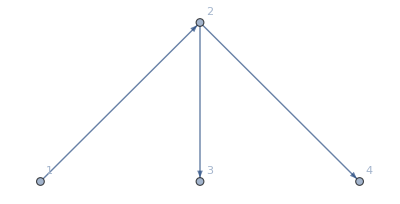
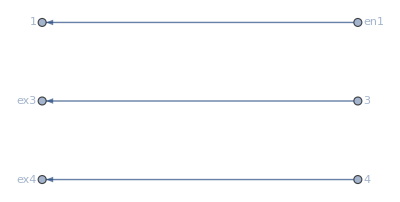
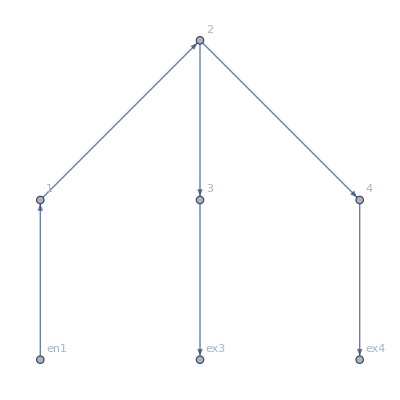
<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,1},{0,0,0,0},{0,0,0,0}},Entrance Vertices and Currents→{{1,1}},Exit Vertices and Terminal Costs→{{3,1},{4,2}},Switching Costs→{},VL→{1,2,3,4},AM→{{0,1,0,0},{0,0,1,1},{0,0,0,0},{0,0,0,0}},EVC→{{1,1}},EVTC→{{3,1},{4,2}},SC→{},BG→-Graphics-,EntranceVertices→{1},InwardVertices→<|1→en1|>,ExitVertices→{3,4},OutwardVertices→<|3→ex3,4→ex4|>,InEdges→{en1->1},OutEdges→{3->ex3,4->ex4},AuxiliaryGraph→-Graphics-,FG→-Graphics-,EL→{1->2,2->3,2->4,3->ex3,4->ex4,en1->1},BEL→{1->2,2->3,2->4},FVL→{1,2,3,4,en1,ex3,ex4},jargs→{{1,1->2},{2,1->2},{2,2->3},{3,2->3},{2,2->4},{4,2->4},{3,3->ex3},{ex3,3->ex3},{4,4->ex4},{ex4,4->ex4},{en1,en1->1},{1,en1->1}},uargs→{{1,1->2},{2,1->2},{2,2->3},{3,2->3},{2,2->4},{4,2->4},{3,3->ex3},{ex3,3->ex3},{4,4->ex4},{ex4,4->ex4},{en1,en1->1},{1,en1->1}},AllTransitions→{{1,1->2,en1->1},{1,en1->1,1->2},{2,1->2,2->3},{2,1->2,2->4},{2,2->3,1->2},{2,2->3,2->4},{2,2->4,1->2},{2,2->4,2->3},{3,2->3,3->ex3},{3,3->ex3,2->3},{4,2->4,4->ex4},{4,4->ex4,2->4}},EntryArgs→{{1,en1->1}},EntryDataAssociation→<|{1,en1->1}→1|>,ExitCosts→<|ex3→1,ex4→2|>,js→{j1,j2,j3,j4,j5,j6,j7,j8,j9,j10,j11,j12},jvars→<|{1,1->2}→j1,{2,1->2}→j2,{2,2->3}→j3,{3,2->3}→j4,{2,2->4}→j5,{4,2->4}→j6,{3,3->ex3}→j7,{ex3,3->ex3}→j8,{4,4->ex4}→j9,{ex4,4->ex4}→j10,{en1,en1->1}→j11,{1,en1->1}→j12|>,us→{u1,u2,u3,u4,u5,u6,u7,u8,u9,u10,u11,u12},uvars→<|{1,1->2}→u1,{2,1->2}→u2,{2,2->3}→u3,{3,2->3}→u4,{2,2->4}→u5,{4,2->4}→u6,{3,3->ex3}→u7,{ex3,3->ex3}→u8,{4,4->ex4}→u9,{ex4,4->ex4}→u10,{en1,en1->1}→u11,{1,en1->1}→u12|>,jts→{jt1,jt2,jt3,jt4,jt5,jt6,jt7,jt8,jt9,jt10,jt11,jt12},jtvars→<|{1,1->2,en1->1}→jt1,{1,en1->1,1->2}→jt2,{2,1->2,2->3}→jt3,{2,1->2,2->4}→jt4,{2,2->3,1->2}→jt5,{2,2->3,2->4}→jt6,{2,2->4,1->2}→jt7,{2,2->4,2->3}→jt8,{3,2->3,3->ex3}→jt9,{3,3->ex3,2->3}→jt10,{4,2->4,4->ex4}→jt11,{4,4->ex4,2->4}→jt12|>,SignedCurrents→<|1->2→-j1+j2,2->3→-j3+j4,2->4→-j5+j6|>,SwitchingCosts→<|{1,1->2,en1->1}→0,{1,en1->1,1->2}→0,{2,1->2,2->3}→0,{2,1->2,2->4}→0,{2,2->3,1->2}→0,{2,2->3,2->4}→0,{2,2->4,1->2}→0,{2,2->4,2->3}→0,{3,2->3,3->ex3}→0,{3,3->ex3,2->3}→0,{4,2->4,4->ex4}→0,{4,4->ex4,2->4}→0|>,EqPosJs→j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0&&j11≥0&&j12≥0,EqPosJts→jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0&&jt5≥0&&jt6≥0&&jt7≥0&&jt8≥0&&jt9≥0&&jt10≥0&&jt11≥0&&jt12≥0,EqCurrentCompCon→(j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0)&&(j11==0||j12==0),EqTransitionCompCon→(jt1==0||jt2==0)&&(jt10==0||jt9==0)&&(jt11==0||jt12==0)&&(jt3==0||jt5==0)&&(jt4==0||jt7==0)&&(jt6==0||jt8==0),NoDeadEnds→{{1,1->2},{1,en1->1},{2,1->2},{2,2->3},{2,2->4},{3,2->3},{3,3->ex3},{4,2->4},{4,4->ex4}},EqBalanceSplittingCurrents→j1==jt1&&j12==jt2&&j2==jt3+jt4&&j3==jt5+jt6&&j5==jt7+jt8&&j4==jt9&&j7==jt10&&j6==jt11&&j9==jt12,BalanceSplittingCurrents→{j1-jt1,j12-jt2,j2-jt3-jt4,j3-jt5-jt6,j5-jt7-jt8,j4-jt9,j7-jt10,j6-jt11,j9-jt12},NoDeadStarts→{{2,1->2},{en1,en1->1},{1,1->2},{3,2->3},{4,2->4},{2,2->3},{ex3,3->ex3},{2,2->4},{ex4,4->ex4}},RuleBalanceGatheringCurrents→<|j2→jt2,j11→jt1,j1→jt5+jt7,j4→jt3+jt8,j6→jt4+jt6,j3→jt10,j8→jt9,j5→jt12,j10→jt11|>,BalanceGatheringCurrents→{-j2+jt2,-j11+jt1,-j1+jt5+jt7,-j4+jt3+jt8,-j6+jt4+jt6,-j3+jt10,-j8+jt9,-j5+jt12,-j10+jt11},EqBalanceGatheringCurrents→j2==jt2&&j11==jt1&&j1==jt5+jt7&&j4==jt3+jt8&&j6==jt4+jt6&&j3==jt10&&j8==jt9&&j5==jt12&&j10==jt11,EqEntryIn→{j12==1},RuleEntryOut→<|j11→0|>,RuleExitCurrentsIn→<|j7→0,j9→0|>,RuleExitValues→<|u8→1,u10→2|>,EqValueAuxiliaryEdges→u11==u12&&u7==u8&&u9==u10,OutRules→{{3,3->ex3,1->2}→∞,{3,3->ex3,2->3}→∞,{3,3->ex3,2->4}→∞,{3,3->ex3,3->ex3}→∞,{3,3->ex3,4->ex4}→∞,{3,3->ex3,en1->1}→∞,{4,4->ex4,1->2}→∞,{4,4->ex4,2->3}→∞,{4,4->ex4,2->4}→∞,{4,4->ex4,3->ex3}→∞,{4,4->ex4,4->ex4}→∞,{4,4->ex4,en1->1}→∞},InRules→{{1,1->2,en1->1}→∞,{1,en1->1,en1->1}→∞},EqSwitchingByVertex→{u1≤u12&&u12≤u1,u2≤u3&&u2≤u5&&u3≤u2&&u3≤u5&&u5≤u2&&u5≤u3,u4≤u7&&u7≤u4,u6≤u9&&u9≤u6},EqCompCon→(jt1==0||-u1+u12==0)&&(jt2==0||u1-u12==0)&&(jt3==0||-u2+u3==0)&&(jt4==0||-u2+u5==0)&&(jt5==0||u2-u3==0)&&(jt6==0||-u3+u5==0)&&(jt7==0||u2-u5==0)&&(jt8==0||u3-u5==0)&&(jt9==0||-u4+u7==0)&&(jt10==0||u4-u7==0)&&(jt11==0||-u6+u9==0)&&(jt12==0||u6-u9==0),Nlhs→{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6},CostArgs→<|{1,1->2}→Identity,{2,1->2}→Identity,{2,2->3}→Identity,{3,2->3}→Identity,{2,2->4}→Identity,{4,2->4}→Identity,{3,3->ex3}→Identity,{ex3,3->ex3}→(0&),{4,4->ex4}→Identity,{ex4,4->ex4}→(0&),{en1,en1->1}→Identity,{1,en1->1}→(0&),{1,1->2,en1->1}→(10^10&),{1,en1->1,1->2}→(0&),{2,1->2,2->3}→(0&),{2,1->2,2->4}→(0&),{2,2->3,1->2}→(0&),{2,2->3,2->4}→(0&),{2,2->4,1->2}→(0&),{2,2->4,2->3}→(0&),{3,2->3,3->ex3}→(0&),{3,3->ex3,2->3}→(10^10&),{4,2->4,4->ex4}→(0&),{4,4->ex4,2->4}→(10^10&)|>,Nrhs→{-j1+j2-IntM[-j1+j2,1->2],-j3+j4-IntM[-j3+j4,2->3],-j5+j6-IntM[-j5+j6,2->4]}|>

```mathematica
d2e
```

### This is the correct solution, since the current should split equally!

```mathematica
(rule=CriticalCongestionSolver2[d2e=D2E[Data/.{I1->65,U1->45,U2->0}]])//AbsoluteTiming
```

D2E: Variables are all set

Second check:

D2E: CleanEqualities for the values at the auxiliary edges

D2E: Assembled most elements of the system

D2E: CleanEqualities for the switching conditions on each vertex

D2E: CleanEqualities for the complementary conditions (given the rules)

D2E: CleanEqualities for the balance conditions in terms of (mostly) transition currents

D2E: CleanEqualities for the (non) critical case equations

D2E: D2E is finished!

CCS2: EliminateVarsSimplify for the us

CCS2: Finished with the us!

CCS2: Finished with the js!

{0.069327,<|u1→120,u2→55,u3→55,u4→45,u5→55,u6→0,u7→45,u8→45,u9→0,u10→0,u11→120,u12→120,j1→0,j2→65,j3→0,j4→10,j5→0,j6→55,j7→0,j8→10,j9→0,j10→55,j11→0,j12→65|>}

```mathematica
d2e
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,1},{0,0,0,0},{0,0,0,0}},Entrance Vertices and Currents→{{1,2}},Exit Vertices and Terminal Costs→{{3,5},{4,5}},Switching Costs→{},BG→-Graphics-,InEdges→{en1->1},OutEdges→{3->ex3,4->ex4},FG→-Graphics-,jvars→<|{1,1->2}→j1,{2,1->2}→j2,{2,2->3}→j3,{3,2->3}→j4,{2,2->4}→j5,{4,2->4}→j6,{3,3->ex3}→j7,{ex3,3->ex3}→j8,{4,4->ex4}→j9,{ex4,4->ex4}→j10,{en1,en1->1}→j11,{1,en1->1}→j12|>,jtvars→<|{1,1->2,en1->1}→jt1,{1,en1->1,1->2}→jt2,{2,1->2,2->3}→jt3,{2,1->2,2->4}→jt4,{2,2->3,1->2}→jt5,{2,2->3,2->4}→jt6,{2,2->4,1->2}→jt7,{2,2->4,2->3}→jt8,{3,2->3,3->ex3}→jt9,{3,3->ex3,2->3}→jt10,{4,2->4,4->ex4}→jt11,{4,4->ex4,2->4}→jt12|>,uvars→<|{1,1->2}→u1,{2,1->2}→u2,{2,2->3}→u3,{3,2->3}→u4,{2,2->4}→u5,{4,2->4}→u6,{3,3->ex3}→u7,{ex3,3->ex3}→u8,{4,4->ex4}→u9,{ex4,4->ex4}→u10,{en1,en1->1}→u11,{1,en1->1}→u12|>,costpluscurrents→<|cpc1→-j1+j2-IntM[-j1+j2,1->2],cpc2→-j3+j4-IntM[-j3+j4,2->3],cpc3→-j5+j6-IntM[-j5+j6,2->4]|>,jays→<|1->2→-j1+j2,2->3→-j3+j4,2->4→-j5+j6|>,AllOr→(2-jt4==0||-jt11+jt4==0)&&(jt4==0||jt11-jt4==0)&&(jt11-jt4==0||-jt11+jt4==0)&&u1-u11==0&&(2-jt11==0||5-u4==0)&&(jt11==0||5-u6==0),AllIneq→2-jt11≥0&&jt11≥0&&2-jt11≥0&&jt11≥0&&2-jt4≥0&&jt4≥0&&-jt11+jt4≥0&&jt11-jt4≥0&&jt11-jt4≥0&&-jt11+jt4≥0&&2-jt11≥0&&jt11≥0&&u1≥u11&&u4≤5&&u6≤5,EqPosJs→j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0&&j11≥0&&j12≥0,EqCurrentCompCon→(j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0)&&(j11==0||j12==0),EqTransitionCompCon→(jt1==0||jt2==0)&&(jt10==0||jt9==0)&&(jt11==0||jt12==0)&&(jt3==0||jt5==0)&&(jt4==0||jt7==0)&&(jt6==0||jt8==0),EqAllAll→(2-jt4==0||-jt11+jt4==0)&&(jt4==0||jt11-jt4==0)&&(jt11-jt4==0||-jt11+jt4==0)&&u1-u11==0&&(2-jt11==0||5-u4==0)&&(jt11==0||5-u6==0)&&2-jt11≥0&&jt11≥0&&2-jt11≥0&&jt11≥0&&2-jt4≥0&&jt4≥0&&-jt11+jt4≥0&&jt11-jt4≥0&&jt11-jt4≥0&&-jt11+jt4≥0&&2-jt11≥0&&jt11≥0&&u1≥u11&&u4≤5&&u6≤5,BoundaryRules→<|j2→2,j11→0,j1→0,j4→2-jt11,j6→jt11,j3→0,j8→2-jt11,j5→0,j10→jt11,j12→2,u8→5,u10→5,u3→u2,u5→u2,jt1→0,jt10→0,jt12→0,u12→u11,u7→5,u9→5,j7→0,j9→0,jt2→2,jt3→2-jt4,jt5→-jt11+jt4,jt6→jt11-jt4,jt7→jt11-jt4,jt8→-jt11+jt4,jt9→2-jt11|>,InitRules→<|j2→2,j11→0,j1→0,j4→2-jt11,j6→jt11,j3→0,j8→2-jt11,j5→0,j10→jt11,j12→2,u8→5,u10→5,u3→u2,u5→u2,jt1→0,jt10→0,jt12→0,u12→u11,u7→5,u9→5,j7→0,j9→0,jt2→2,jt3→2-jt4,jt5→-jt11+jt4,jt6→jt11-jt4,jt7→jt11-jt4,jt8→-jt11+jt4,jt9→2-jt11|>,RulesCriticalCase→<|j2→2,j11→0,j1→0,j4→2-jt11,j6→jt11,j3→0,j8→2-jt11,j5→0,j10→jt11,j12→2,u8→5,u10→5,u3→-2+u1,u5→-2+u1,jt1→0,jt10→0,jt12→0,u12→u11,u7→5,u9→5,j7→0,j9→0,jt2→2,jt3→2-jt4,jt5→-jt11+jt4,jt6→jt11-jt4,jt7→jt11-jt4,jt8→-jt11+jt4,jt9→2-jt11,u2→-2+u1,u4→-4+jt11+u1,u6→-2-jt11+u1|>,RulesCriticalCase1→{{u2→j1-j2+u1,u4→j1-j2+j3-j4+u1,u6→j1-j2+j5-j6+u1}},RuleEntryIn→{j12→2},Nlhs→{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6},MinimalTimeRhs→{0,0,0},EqCriticalCase→-j1+j2-u1+u2==0&&-j3+j4-u2+u4==0&&-j5+j6-u2+u6==0,EqNonCritical→-j1+j2-u1+u2==cpc1&&-j3+j4-u2+u4==cpc2&&-j5+j6-u2+u6==cpc3,RuleNonCritical→<|j2→2,j11→0,j1→0,j4→2-jt11,j6→jt11,j3→0,j8→2-jt11,j5→0,j10→jt11,j12→2,u8→5,u10→5,u3→-2+cpc1+u1,u5→-2+cpc1+u1,jt1→0,jt10→0,jt12→0,u12→u11,u7→5,u9→5,j7→0,j9→0,jt2→2,jt3→2-jt4,jt5→-jt11+jt4,jt6→jt11-jt4,jt7→jt11-jt4,jt8→-jt11+jt4,jt9→2-jt11,u2→-2+cpc1+u1,u4→-4+cpc1+cpc2+jt11+u1,u6→-2+cpc1+cpc3-jt11+u1|>,RuleNonCritical1→{{u2→cpc1+j1-j2+u1,u4→cpc1+cpc2+j1-j2+j3-j4+u1,u6→cpc1+cpc3+j1-j2+j5-j6+u1}},EqSwitchingConditions→u1≥u12&&u2==u5&&u3==u5&&u4≤u7&&u6≤u9,EqValueAuxiliaryEdges→u12==u11&&u8==u7&&u10==u9,EqBalanceSplittingCurrents→j1==jt1&&j12==jt2&&j2==jt3+jt4&&j3==jt5+jt6&&j5==jt7+jt8&&j4==jt9&&j7==jt10&&j6==jt11&&j9==jt12,EqBalanceGatheringCurrents→j2==jt2&&j11==jt1&&j1==jt5+jt7&&j4==jt3+jt8&&j6==jt4+jt6&&j3==jt10&&j8==jt9&&j5==jt12&&j10==jt11,Nrhs→{-j1+j2-IntM[-j1+j2,1->2],-j3+j4-IntM[-j3+j4,2->3],-j5+j6-IntM[-j5+j6,2->4]}|>

## Non-critical congestion

```mathematica
Cost[current_,edge_]
```

IntM[current_,edge_]

```mathematica
Cost[a_,b_]:= -a
```

```mathematica
Cost[a_,b_]:= 0
```

```mathematica
d2e=D2E[Data/.{I1->2,U1->5,U2->5}];
```

```mathematica
alpha =0.9;
FFR=FixedPoint[FixedReduce2[d2e],<||>,9]
```

EliminateVarsSimplify for the us

Finished with the us!

Done!

non critical rules with j values:
<|j2→2,j11→0,j1→0,j4→2-jt11,j6→jt11,j3→0,j8→2-jt11,j5→0,j10→jt11,j12→2,u8→5,u10→5,u3→-959279519/500000000+u1,u5→-959279519/500000000+u1,jt1→0,jt10→0,jt12→0,u12→u11,u7→5,u9→5,j7→0,j9→0,jt2→2,jt3→2-jt4,jt5→-jt11+jt4,jt6→jt11-jt4,jt7→jt11-jt4,jt8→-jt11+jt4,jt9→2-jt11,u2→-959279519/500000000+u1,u4→-7870426059/2000000000+jt11+u1,u6→-3870426059/2000000000-jt11+u1|>

EliminateVarsSimplify for the us

Finished with the us!

Done!

returned uvalues: 
{7.93521,6.01665,6.01665,5.,6.01665,5.,5.,5.,5.,5.,7.93521,7.93521,0.,2.,0.,1.,0.,1.,0.,1.,0.,1.,0.,2.}

non critical rules with j values:
<|j2→2,j11→0,j1→0,j4→2-jt11,j6→jt11,j3→0,j8→2-jt11,j5→0,j10→jt11,j12→2,u8→5,u10→5,u3→-959279519/500000000+u1,u5→-959279519/500000000+u1,jt1→0,jt10→0,jt12→0,u12→u11,u7→5,u9→5,j7→0,j9→0,jt2→2,jt3→2-jt4,jt5→-jt11+jt4,jt6→jt11-jt4,jt7→jt11-jt4,jt8→-jt11+jt4,jt9→2-jt11,u2→-959279519/500000000+u1,u4→-7870426059/2000000000+jt11+u1,u6→-3870426059/2000000000-jt11+u1|>

EliminateVarsSimplify for the us

Finished with the us!

Done!

returned uvalues: 
{7.93521,6.01665,6.01665,5.,6.01665,5.,5.,5.,5.,5.,7.93521,7.93521,0.,2.,0.,1.,0.,1.,0.,1.,0.,1.,0.,2.}

<|u1→15870426059/2000000000,u2→12033307983/2000000000,u3→12033307983/2000000000,u4→5,u5→12033307983/2000000000,u6→5,u7→5,u8→5,u9→5,u10→5,u11→15870426059/2000000000,u12→15870426059/2000000000,j1→0,j2→2,j3→0,j4→1,j5→0,j6→1,j7→0,j8→1,j9→0,j10→1,j11→0,j12→2|>

```mathematica
alpha =0.5;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

EliminateVarsSimplify for the us

Finished with the us!

Done!

EliminateVarsSimplify for the us

Finished with the us!

Done!

EliminateVarsSimplify for the us

Finished with the us!

Done!

<|u1→77491808883/10000000000,u2→60738049571/10000000000,u3→60738049571/10000000000,u4→5,u5→60738049571/10000000000,u6→5,u7→5,u8→5,u9→5,u10→5,u11→77491808883/10000000000,u12→77491808883/10000000000,j1→0,j2→2,j3→0,j4→1,j5→0,j6→1,j7→0,j8→1,j9→0,j10→1,j11→0,j12→2|>

```mathematica
alpha =1;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

EliminateVarsSimplify for the us

Finished with the us!

Done!

EliminateVarsSimplify for the us

Finished with the us!

Done!

<|u1→8,u2→6,u3→6,u4→5,u5→6,u6→5,u7→5,u8→5,u9→5,u10→5,u11→8,u12→8,j1→0,j2→2,j3→0,j4→1,j5→0,j6→1,j7→0,j8→1,j9→0,j10→1,j11→0,j12→2|>

```mathematica
alpha =1.5;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

EliminateVarsSimplify for the us

Finished with the us!

Done!

EliminateVarsSimplify for the us

Finished with the us!

Done!

EliminateVarsSimplify for the us

Finished with the us!

Done!

<|u1→85493471337/10000000000,u2→58974978013/10000000000,u3→58974978013/10000000000,u4→5,u5→58974978013/10000000000,u6→5,u7→5,u8→5,u9→5,u10→5,u11→85493471337/10000000000,u12→85493471337/10000000000,j1→0,j2→2,j3→0,j4→1,j5→0,j6→1,j7→0,j8→1,j9→0,j10→1,j11→0,j12→2|>

```mathematica
alpha =2;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

EliminateVarsSimplify for the us

Finished with the us!

Done!

EliminateVarsSimplify for the us

Finished with the us!

Done!

EliminateVarsSimplify for the us

Finished with the us!

Done!

<|u1→41/4,u2→23/4,u3→23/4,u4→5,u5→23/4,u6→5,u7→5,u8→5,u9→5,u10→5,u11→41/4,u12→41/4,j1→0,j2→2,j3→0,j4→1,j5→0,j6→1,j7→0,j8→1,j9→0,j10→1,j11→0,j12→2|>

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,1},{0,0,0,0},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1},{4,U2}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->2,U1->5,U2->5}];//Timing
```

DataToEquations: Triangle inequalities for switching costs: {}
DataToEquations: Reduced: True

The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: The system is:
NonNegative[j732]&&NonNegative[2-j732]&&NonNegative[j732]&&NonNegative[2-j732]&&NonNegative[jt745]&&NonNegative[2-jt745]&&NonNegative[j732-jt745]&&NonNegative[-j732+jt745]&&NonNegative[-j732+jt745]&&NonNegative[j732-jt745]&&NonNegative[j732]&&NonNegative[2-j732]&&NonNegative[2-u755+u756]&&NonNegative[2-u755+u757]&&NonNegative[-2+u755-u756]&&NonNegative[-u756+u757]&&NonNegative[-2+u755-u757]&&NonNegative[u756-u757]&&NonNegative[5+j732-u756]&&NonNegative[7-j732-u757]&&(jt745==0||j732-jt745==0)&&(2-jt745==0||-j732+jt745==0)&&(-j732+jt745==0||j732-jt745==0)&&(jt745==0||2-u755+u756==0)&&(2-jt745==0||2-u755+u757==0)&&(j732-jt745==0||-2+u755-u756==0)&&(-j732+jt745==0||-u756+u757==0)&&(-j732+jt745==0||-2+u755-u757==0)&&(j732-jt745==0||u756-u757==0)&&(j732==0||5+j732-u756==0)&&(2-j732==0||7-j732-u757==0)
and the rules are:
<|j731→2,j733→2-j732,j734→j732,j735→2-j732,j736→2,j737→0,j738→0,j739→0,j740→0,j741→0,j742→0,jt743→0,jt744→2,jt746→2-jt745,jt747→j732-jt745,jt748→-j732+jt745,jt749→-j732+jt745,jt750→j732-jt745,jt751→j732,jt752→0,jt753→2-j732,jt754→0,u758→5,u759→5,u761→-2+u755,u762→-j732+u756,u763→-2+j732+u757,u764→5,u765→5,u766→u755,u760→u755|>

DataToEquations: It took 0.045068 seconds to reduce with NewReduce!

DataToEquations: After NewReduce, the system is:
j732==1&&jt745==1&&u755==8&&u756==6&&u757==6
and the rules are:
<|j731→2,j733→2-j732,j734→j732,j735→2-j732,j736→2,j737→0,j738→0,j739→0,j740→0,j741→0,j742→0,jt743→0,jt744→2,jt746→2-jt745,jt747→j732-jt745,jt748→-j732+jt745,jt749→-j732+jt745,jt750→j732-jt745,jt751→j732,jt752→0,jt753→2-j732,jt754→0,u758→5,u759→5,u761→-2+u755,u762→-j732+u756,u763→-2+j732+u757,u764→5,u765→5,u766→u755,u760→u755|>

DataToEquations: Critical congestion solved.

all ok? up to here?

{j731-j737+IntM[j731-j737,1->2],j732-j738+IntM[j732-j738,2->3],j733-j739+IntM[j733-j739,2->4]}

DataToEquations: Done.

{0.070324,Null}

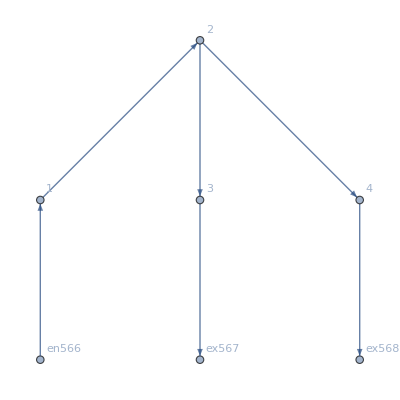

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j569→2,j570→2,j571→0,j572→2,j573→0,j574→2,j575→0,j576→0,j577→0,j578→0,j579→0,j580→0,jt581→0,jt582→2,jt583→2,jt584→0,jt585→0,jt586→0,jt587→0,jt588→0,jt589→2,jt590→0,jt591→0,jt592→0,u593→6,u594→4,u595→4,u596→2,u597→5,u598→6,u599→4,u600→2,u601→4,u602→2,u603→5,u604→6|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: nonlinear: 
j569-j575-u593+u599==0.517166&&j570-j576-u594+u600==0.517166&&j571-j577-u595+u601==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: nonlinear: 
j569-j575-u593+u599==0.517166&&j570-j576-u594+u600==0.517166&&j571-j577-u595+u601==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j569→2,j570→2.,j571→0.,j572→2.,j573→0.,j574→2,j575→0,j576→0,j577→0,j578→0,j579→0,j580→0,jt581→0,jt582→2,jt583→2.,jt584→0.,jt585→0.,jt586→0.,jt587→0.,jt588→0.,jt589→2.,jt590→0,jt591→0.,jt592→0,u593→4.96567,u594→3.48283,u595→3.48283,u596→2,u597→5,u598→4.96567,u599→3.48283,u600→2.,u601→3.48283,u602→2,u603→5,u604→4.96567|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.71948×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.71948×10^-16

<|j14→2.,j15→1.,j16→1.,j17→1.,j18→1.,j19→2.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,j25→0.,jt26→0.,jt27→2.,jt28→1.,jt29→1.,jt30→0.,jt31→0.,jt32→0,jt33→0.,jt34→1.,jt35→0.,jt36→1.,jt37→0.,u38→6.82592,u39→5.72685,u40→5.72685,u41→5.,u42→5.,u43→6.82592,u44→5.72685,u45→5.,u46→5.,u47→5.,u48→5.,u49→6.82592|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.71028×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.71028×10^-16

<|j14→2.,j15→1.,j16→1.,j17→1.,j18→1.,j19→2.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,j25→0.,jt26→0.,jt27→2.,jt28→1.,jt29→1.,jt30→0.,jt31→0.,jt32→0,jt33→0.,jt34→1.,jt35→0.,jt36→1.,jt37→0.,u38→6.99482,u39→5.77321,u40→5.77321,u41→5.,u42→5.,u43→6.99482,u44→5.77321,u45→5.,u46→5.,u47→5.,u48→5.,u49→6.99482|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.43896×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.43896×10^-16

<|j14→2.,j15→1.,j16→1.,j17→1.,j18→1.,j19→2.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,j25→0.,jt26→0.,jt27→2.,jt28→1.,jt29→1.,jt30→0.,jt31→0.,jt32→0,jt33→0.,jt34→1.,jt35→0.,jt36→1.,jt37→0.,u38→7.79269,u39→5.9592,u40→5.9592,u41→5.,u42→5.,u43→7.79269,u44→5.9592,u45→5.,u46→5.,u47→5.,u48→5.,u49→7.79269|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j731-j737-u755+u761==0&&j732-j738-u756+u762==0&&j733-j739-u757+u763==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[2.71948×10^-15,ComplexInfinity]

<|j731→2,j732→1,j733→1,j734→1,j735→1,j736→2,j737→0,j738→0,j739→0,j740→0,j741→0,j742→0,jt743→0,jt744→2,jt745→1,jt746→1,jt747→0,jt748→0,jt749→0,jt750→0,jt751→1,jt752→0,jt753→1,jt754→0,u755→8,u756→6,u757→6,u758→5,u759→5,u760→8,u761→6,u762→5,u763→5,u764→5,u765→5,u766→8|>

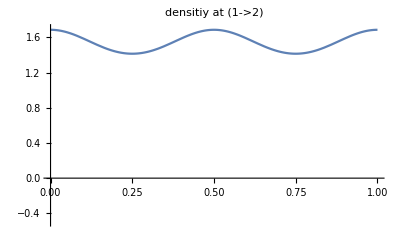
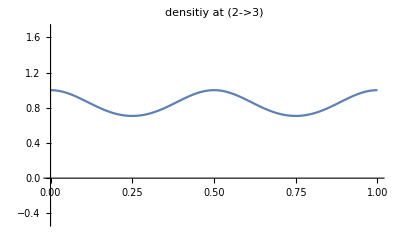
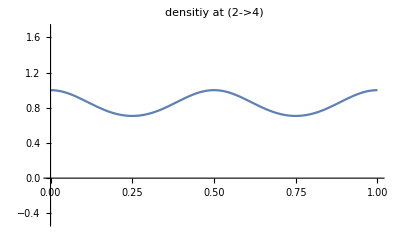

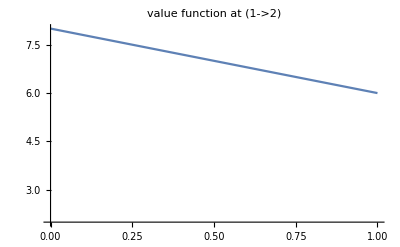
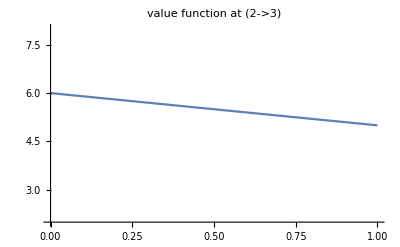
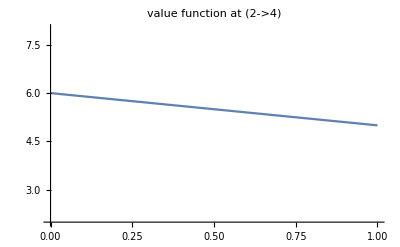

```mathematica
FFR=MFGEquations["criticalreduced1"][[2]];
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->"densitiy at "#,PlotRange-> {-.5,1.7}]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->"value function at "#,PlotRange-> {2,8}]&/@MFGEquations["BEL"]
```

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.69185×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.69185×10^-16

<|j14→2.,j15→1.,j16→1.,j17→1.,j18→1.,j19→2.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,j25→0.,jt26→0.,jt27→2.,jt28→1.,jt29→1.,jt30→0.,jt31→0.,jt32→0,jt33→0.,jt34→1.,jt35→0.,jt36→1.,jt37→0.,u38→8.53675,u39→6.0941,u40→6.0941,u41→5.,u42→5.,u43→8.53675,u44→6.0941,u45→5.,u46→5.,u47→5.,u48→5.,u49→8.53675|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.0229×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14578×10^-15

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14578×10^-15

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14578×10^-15

«6 more identical outputs»

<|j14→2.,j15→1.,j16→1.,j17→1.,j18→1.,j19→2.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,j25→0.,jt26→0.,jt27→2.,jt28→1.,jt29→1.,jt30→0.,jt31→0.,jt32→0,jt33→0.,jt34→1.,jt35→0.,jt36→1.,jt37→0.,u38→9.92172,u39→6.27899,u40→6.27899,u41→5.,u42→5.,u43→9.92172,u44→6.27899,u45→5.,u46→5.,u47→5.,u48→5.,u49→9.92172|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10(*,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)*)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.53329×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.53329×10^-16

<|j14→2.,j15→1.,j16→1.,j17→1.,j18→1.,j19→2.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,j25→0.,jt26→0.,jt27→2.,jt28→1.,jt29→1.,jt30→0.,jt31→0.,jt32→0,jt33→0.,jt34→1.,jt35→0.,jt36→1.,jt37→0.,u38→10.7031,u39→6.35738,u40→6.35738,u41→5.,u42→5.,u43→10.7031,u44→6.35738,u45→5.,u46→5.,u47→5.,u48→5.,u49→10.7031|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.81446×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.62458×10^-16

<|j14→2.,j15→1.,j16→1.,j17→1.,j18→1.,j19→2.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,j25→0.,jt26→0.,jt27→2.,jt28→1.,jt29→1.,jt30→0.,jt31→0.,jt32→0,jt33→0.,jt34→1.,jt35→0.,jt36→1.,jt37→0.,u38→13.5434,u39→6.55247,u40→6.55247,u41→5.,u42→5.,u43→13.5434,u44→6.55247,u45→5.,u46→5.,u47→5.,u48→5.,u49→13.5434|>

```mathematica
<|j14->2.,j15->2.,j16->0.,j17->2.,j18->0.,j19->2.,j20->0.,j21->0.,j22->0.,j23->0.,j24->0.,j25->0.,jt26->0.,jt27->2.,jt28->2.,jt29->0.,jt30->0.,jt31->0.,jt32->0,jt33->0.,jt34->2.,jt35->0.,jt36->0.,jt37->0.,u38->13.990914203088625,u39->7.,u40->7.,u41->5.,u42->5.,u43->13.990914203088625,u44->7.,u45->5.,u46->2.009085796911375,u47->5.,u48->5.,u49->13.990914203088625|>;
```

```mathematica
<|j14->2.,j15->1.000000000000022,j16->0.999999999999978,j17->1.000000000000022,j18->0.999999999999978,j19->2.,j20->0.,j21->0.,j22->0.,j23->0.,j24->0.,j25->0.,jt26->0.,jt27->2.,jt28->1.000000000000022,jt29->0.999999999999978,jt30->0.,jt31->0.,jt32->0,jt33->0.,jt34->1.000000000000022,jt35->0.,jt36->0.999999999999978,jt37->0.,u38->13.543381675652178,u39->6.552467472563553,u40->6.552467472563553,u41->5.,u42->5.,u43->13.543381675652178,u44->6.552467472563553,u45->4.999999999999999,u46->5.,u47->5.,u48->5.,u49->13.543381675652178|>
```

```mathematica
<|j14->2.,j15->1.0000000000000002,j16->0.9999999999999998,j17->1.0000000000000002,j18->0.9999999999999998,j19->2.,j20->0.,j21->0.,j22->0.,j23->0.,j24->0.,j25->0.,jt26->0.,jt27->2.,jt28->1.0000000000000002,jt29->0.9999999999999998,jt30->0.,jt31->0.,jt32->0,jt33->0.,jt34->1.0000000000000002,jt35->0.,jt36->0.9999999999999998,jt37->0.,u38->13.543381675652178,u39->6.552467472563554,u40->6.552467472563554,u41->5.,u42->5.,u43->13.543381675652178,u44->6.552467472563554,u45->5.000000000000001,u46->5.,u47->5.,u48->5.,u49->13.543381675652178|>;
```

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.94896×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.94896×10^-17

<|j14→2.,j15→1.,j16→1.,j17→1.,j18→1.,j19→2.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,j25→0.,jt26→0.,jt27→2.,jt28→1.,jt29→1.,jt30→0.,jt31→0.,jt32→0,jt33→0.,jt34→1.,jt35→0.,jt36→1.,jt37→0.,u38→16.5708,u39→6.6767,u40→6.6767,u41→5.,u42→5.,u43→16.5708,u44→6.6767,u45→5.,u46→5.,u47→5.,u48→5.,u49→16.5708|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.17756×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.17756×10^-17

<|j14→2.,j15→1.,j16→1.,j17→1.,j18→1.,j19→2.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,j25→0.,jt26→0.,jt27→2.,jt28→1.,jt29→1.,jt30→0.,jt31→0.,jt32→0,jt33→0.,jt34→1.,jt35→0.,jt36→1.,jt37→0.,u38→23.1999,u39→6.82668,u40→6.82668,u41→5.,u42→5.,u43→23.1999,u44→6.82668,u45→5.,u46→5.,u47→5.,u48→5.,u49→23.1999|>